```mathematica
SetDirectory[NotebookDirectory[]];
data = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5"];
```

```mathematica
data[[2]]
```

/C01:IMRPhenomXPHM/calibration_envelope/H1

```mathematica
post1 = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5", "/C01:IMRPhenomXPHM/posterior_samples"];
post2 = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5", "/C01:Mixed/posterior_samples"];
post3 = Import["IGWN-GWTC2p1-v2-GW190805_211137_PEDataRelease_mixed_cosmo.h5", "/C01:SEOBNRv4PHM/posterior_samples"];
```

```mathematica
post1[[1]] // Keys
post2[[1]] // Keys
post3[[1]] // Keys
```

{chirp_mass,mass_ratio,a_1,a_2,tilt_1,tilt_2,phi_12,phi_jl,theta_jn,psi,phase,azimuth,zenith,recalib_H1_amplitude_0,recalib_H1_amplitude_1,recalib_H1_amplitude_2,recalib_H1_amplitude_3,recalib_H1_amplitude_4,recalib_H1_amplitude_5,recalib_H1_amplitude_6,recalib_H1_amplitude_7,recalib_H1_amplitude_8,recalib_H1_amplitude_9,recalib_H1_phase_0,recalib_H1_phase_1,recalib_H1_phase_2,recalib_H1_phase_3,recalib_H1_phase_4,recalib_H1_phase_5,recalib_H1_phase_6,recalib_H1_phase_7,recalib_H1_phase_8,recalib_H1_phase_9,recalib_L1_amplitude_0,recalib_L1_amplitude_1,recalib_L1_amplitude_2,recalib_L1_amplitude_3,recalib_L1_amplitude_4,recalib_L1_amplitude_5,recalib_L1_amplitude_6,recalib_L1_amplitude_7,recalib_L1_amplitude_8,recalib_L1_amplitude_9,recalib_L1_phase_0,recalib_L1_phase_1,recalib_L1_phase_2,recalib_L1_phase_3,recalib_L1_phase_4,recalib_L1_phase_5,recalib_L1_phase_6,recalib_L1_phase_7,recalib_L1_phase_8,recalib_L1_phase_9,recalib_V1_amplitude_0,recalib_V1_amplitude_1,recalib_V1_amplitude_2,recalib_V1_amplitude_3,recalib_V1_amplitude_4,recalib_V1_amplitude_5,recalib_V1_amplitude_6,recalib_V1_amplitude_7,recalib_V1_amplitude_8,recalib_V1_amplitude_9,recalib_V1_phase_0,recalib_V1_phase_1,recalib_V1_phase_2,recalib_V1_phase_3,recalib_V1_phase_4,recalib_V1_phase_5,recalib_V1_phase_6,recalib_V1_phase_7,recalib_V1_phase_8,recalib_V1_phase_9,time_jitter,luminosity_distance,geocent_time,recalib_H1_frequency_0,recalib_H1_frequency_1,recalib_H1_frequency_2,recalib_H1_frequency_3,recalib_H1_frequency_4,recalib_H1_frequency_5,recalib_H1_frequency_6,recalib_H1_frequency_7,recalib_H1_frequency_8,recalib_H1_frequency_9,recalib_L1_frequency_0,recalib_L1_frequency_1,recalib_L1_frequency_2,recalib_L1_frequency_3,recalib_L1_frequency_4,recalib_L1_frequency_5,recalib_L1_frequency_6,recalib_L1_frequency_7,recalib_L1_frequency_8,recalib_L1_frequency_9,recalib_V1_frequency_0,recalib_V1_frequency_1,recalib_V1_frequency_2,recalib_V1_frequency_3,recalib_V1_frequency_4,recalib_V1_frequency_5,recalib_V1_frequency_6,recalib_V1_frequency_7,recalib_V1_frequency_8,recalib_V1_frequency_9,log_likelihood,log_prior,total_mass,mass_1,mass_2,ra,dec,symmetric_mass_ratio,iota,spin_1x,spin_1y,spin_1z,spin_2x,spin_2y,spin_2z,phi_1,phi_2,chi_eff,chi_1_in_plane,chi_2_in_plane,chi_p,cos_tilt_1,cos_tilt_2,comoving_distance,H1_matched_filter_snr,H1_optimal_snr,L1_matched_filter_snr,L1_optimal_snr,V1_matched_filter_snr,V1_optimal_snr,H1_matched_filter_abs_snr,H1_matched_filter_snr_angle,L1_matched_filter_abs_snr,L1_matched_filter_snr_angle,V1_matched_filter_abs_snr,V1_matched_filter_snr_angle,redshift,inverted_mass_ratio,mass_1_source,mass_2_source,total_mass_source,chirp_mass_source,final_spin,peak_luminosity,final_mass,final_mass_source,radiated_energy,H1_time,L1_time,V1_time,network_optimal_snr,network_matched_filter_snr,cos_theta_jn,cos_iota,tilt_1_infinity_only_prec_avg,tilt_2_infinity_only_prec_avg,chi_p_2spin,spin_1z_infinity_only_prec_avg,spin_2z_infinity_only_prec_avg,chi_eff_infinity_only_prec_avg,chi_p_infinity_only_prec_avg,beta,psi_J,cos_tilt_1_infinity_only_prec_avg,cos_tilt_2_infinity_only_prec_avg,viewing_angle}

{theta_jn,chirp_mass,cos_tilt_1,psi,total_mass_source,phi_1,chi_eff,dec,radiated_energy,final_spin,geocent_time,phi_12,ra,phi_jl,symmetric_mass_ratio,redshift,log_likelihood,phase,spin_2x,iota,final_mass,cos_tilt_2,a_2,luminosity_distance,a_1,total_mass,mass_2_source,tilt_1,spin_1y,peak_luminosity,mass_ratio,chi_p,spin_1z,chirp_mass_source,phi_2,final_mass_source,mass_2,spin_2z,cos_theta_jn,mass_1,spin_2y,cos_iota,spin_1x,comoving_distance,tilt_2,mass_1_source,inverted_mass_ratio,tilt_1_infinity_only_prec_avg,tilt_2_infinity_only_prec_avg,chi_p_2spin,spin_1z_infinity_only_prec_avg,spin_2z_infinity_only_prec_avg,chi_eff_infinity_only_prec_avg,chi_p_infinity_only_prec_avg,beta,psi_J,cos_tilt_1_infinity_only_prec_avg,cos_tilt_2_infinity_only_prec_avg,viewing_angle}

{mass_1,mass_2,spin_1x,spin_1y,spin_1z,spin_2x,spin_2y,spin_2z,chirp_mass,symmetric_mass_ratio,ra,dec,geocent_time,phase,iota,psi,luminosity_distance,Npts,log_likelihood,p,ps,neff,total_mass,mass_ratio,chi_eff,chi_p,redshift,comoving_distance,inverted_mass_ratio,mass_1_source,mass_2_source,total_mass_source,chirp_mass_source,theta_jn,phi_jl,tilt_1,tilt_2,phi_12,a_1,a_2,phi_1,phi_2,tilt_1_infinity_only_prec_avg,tilt_2_infinity_only_prec_avg,chi_p_2spin,spin_1z_infinity_only_prec_avg,spin_2z_infinity_only_prec_avg,chi_eff_infinity_only_prec_avg,chi_p_infinity_only_prec_avg,beta,psi_J,final_spin,peak_luminosity,final_mass,cos_tilt_1_infinity_only_prec_avg,cos_tilt_2_infinity_only_prec_avg,cos_tilt_1,cos_tilt_2,final_mass_source,radiated_energy,cos_theta_jn,viewing_angle,cos_iota}

```mathematica
#[a] & /@ {<|a-> 0.9, b-> 0|>, <|a-> 0.91, b-> 0.1|>}
```

{0.9,0.91}

```mathematica
<|a-> 0.9, b-> 0|>[a]
```

0.9

```mathematica
<|a-> 0.9, b-> 0|>[a]
```

0.9

```mathematica
dd = Dataset[{<|a-> 0.9, b-> 0|>, <|a-> 0.91, b-> 0.1|>}][a]
```

a[{<|a→0.9,b→0|>,<|a→0.91,b→0.1|>}]

```mathematica
FullForm[dd]
```

Dataset[List[Association[Rule[a,0.9],Rule[b,0]],Association[Rule[a,0.91],Rule[b,0.1]]],TypeSystem`Vector[TypeSystem`Assoc[TypeSystem`AnyType,TypeSystem`Atom[Real],2],2],Association[]]

45.7464

0.932976

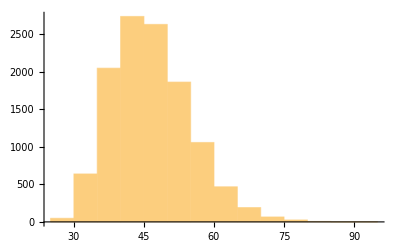
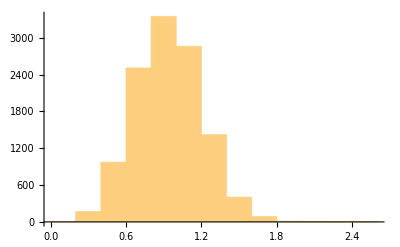

{46.1699,-11.2345,15.4309}

{0.920592,-0.400923,0.431276}

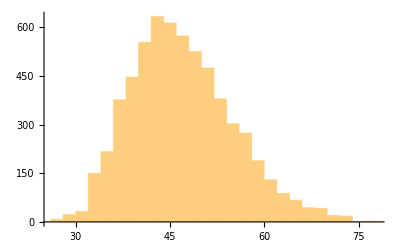
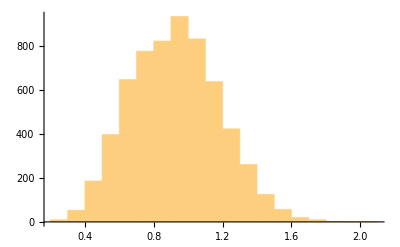

46.6077

0.893883

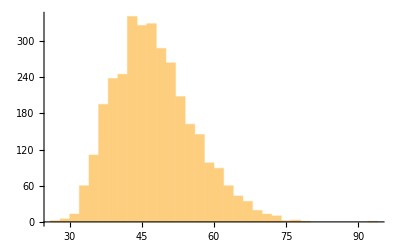
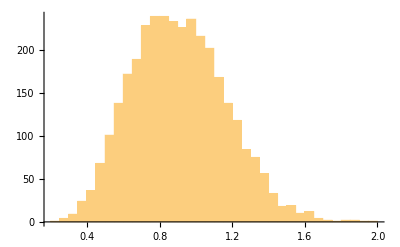

```mathematica
{
  datam1p1 = #["mass_1_source"] & /@ post1;
  Echo@Median[datam1p1];
  Histogram[datam1p1]
,
  datazp1 = #["redshift"] & /@ post1;
  Echo@Median[datazp1];
  Histogram[datazp1]
}

{
  datam1p2 = #["mass_1_source"] & /@ post2;
  Echo[{Median[datam1p2], Quantile[datam1p2, 0.05]- Median[datam1p2], Quantile[datam1p2, 0.95]- Median[datam1p2]}];
  Histogram[datam1p2]
,
  datazp2 = #["redshift"] & /@ post2;
  Echo[{Median[datazp2], Quantile[datazp2, 0.05]- Median[datazp2], Quantile[datazp2, 0.95]- Median[datazp2]}];
  Histogram[datazp2]
}

{
  datam1p3 = #["mass_1_source"] & /@ post3;
  Echo@Median[datam1p3];
  Histogram[datam1p3]
  ,
  datazp3 = #["redshift"] & /@ post3;
  Echo@Median[datazp3];
  Histogram[datazp3]
}
```

```mathematica
datazp3 // Length
```

3305

```mathematica
Keys[post][[1]]
```

{theta_jn,chirp_mass,cos_tilt_1,psi,total_mass_source,phi_1,chi_eff,dec,radiated_energy,final_spin,geocent_time,phi_12,ra,phi_jl,symmetric_mass_ratio,redshift,log_likelihood,phase,spin_2x,iota,final_mass,cos_tilt_2,a_2,luminosity_distance,a_1,total_mass,mass_2_source,tilt_1,spin_1y,peak_luminosity,mass_ratio,chi_p,spin_1z,chirp_mass_source,phi_2,final_mass_source,mass_2,spin_2z,cos_theta_jn,mass_1,spin_2y,cos_iota,spin_1x,comoving_distance,tilt_2,mass_1_source,inverted_mass_ratio,tilt_1_infinity_only_prec_avg,tilt_2_infinity_only_prec_avg,chi_p_2spin,spin_1z_infinity_only_prec_avg,spin_2z_infinity_only_prec_avg,chi_eff_infinity_only_prec_avg,chi_p_infinity_only_prec_avg,beta,psi_J,cos_tilt_1_infinity_only_prec_avg,cos_tilt_2_infinity_only_prec_avg,viewing_angle}

```mathematica
data
```

{/C01:IMRPhenomXPHM/approximant,/C01:IMRPhenomXPHM/calibration_envelope/H1,/C01:IMRPhenomXPHM/calibration_envelope/L1,/C01:IMRPhenomXPHM/calibration_envelope/V1,/C01:IMRPhenomXPHM/config_file/config/accounting,/C01:IMRPhenomXPHM/config_file/config/calibration-model,/C01:IMRPhenomXPHM/config_file/config/catch-waveform-errors,/C01:IMRPhenomXPHM/config_file/config/channel-dict,/C01:IMRPhenomXPHM/config_file/config/coherence-test,/C01:IMRPhenomXPHM/config_file/config/convert-to-flat-in-component-mass,/C01:IMRPhenomXPHM/config_file/config/create-plots,/C01:IMRPhenomXPHM/config_file/config/create-summary,/C01:IMRPhenomXPHM/config_file/config/data-dict,/C01:IMRPhenomXPHM/config_file/config/data-format,/C01:IMRPhenomXPHM/config_file/config/deltaT,/C01:IMRPhenomXPHM/config_file/config/detectors,/C01:IMRPhenomXPHM/config_file/config/distance-marginalization,/C01:IMRPhenomXPHM/config_file/config/distance-marginalization-lookup-table,/C01:IMRPhenomXPHM/config_file/config/duration,/C01:IMRPhenomXPHM/config_file/config/email,/C01:IMRPhenomXPHM/config_file/config/existing-dir,/C01:IMRPhenomXPHM/config_file/config/extra-likelihood-kwargs,/C01:IMRPhenomXPHM/config_file/config/frequency-domain-source-model,/C01:IMRPhenomXPHM/config_file/config/gaussian-noise,/C01:IMRPhenomXPHM/config_file/config/generation-seed,/C01:IMRPhenomXPHM/config_file/config/gps-file,/C01:IMRPhenomXPHM/config_file/config/gps-tuple,/C01:IMRPhenomXPHM/config_file/config/ignore-gwpy-data-quality-check,/C01:IMRPhenomXPHM/config_file/config/injection,/C01:IMRPhenomXPHM/config_file/config/injection-dict,/C01:IMRPhenomXPHM/config_file/config/injection-file,/C01:IMRPhenomXPHM/config_file/config/injection-numbers,/C01:IMRPhenomXPHM/config_file/config/injection-waveform-approximant,/C01:IMRPhenomXPHM/config_file/config/jitter-time,/C01:IMRPhenomXPHM/config_file/config/label,/C01:IMRPhenomXPHM/config_file/config/likelihood-type,/C01:IMRPhenomXPHM/config_file/config/local,/C01:IMRPhenomXPHM/config_file/config/local-generation,/C01:IMRPhenomXPHM/config_file/config/local-plot,/C01:IMRPhenomXPHM/config_file/config/log-directory,/C01:IMRPhenomXPHM/config_file/config/maximum-frequency,/C01:IMRPhenomXPHM/config_file/config/minimum-frequency,/C01:IMRPhenomXPHM/config_file/config/n-parallel,/C01:IMRPhenomXPHM/config_file/config/n-simulation,/C01:IMRPhenomXPHM/config_file/config/online-pe,/C01:IMRPhenomXPHM/config_file/config/osg,/C01:IMRPhenomXPHM/config_file/config/outdir,/C01:IMRPhenomXPHM/config_file/config/periodic-restart-time,/C01:IMRPhenomXPHM/config_file/config/phase-marginalization,/C01:IMRPhenomXPHM/config_file/config/plot-calibration,/C01:IMRPhenomXPHM/config_file/config/plot-corner,/C01:IMRPhenomXPHM/config_file/config/plot-format,/C01:IMRPhenomXPHM/config_file/config/plot-marginal,/C01:IMRPhenomXPHM/config_file/config/plot-skymap,/C01:IMRPhenomXPHM/config_file/config/plot-waveform,/C01:IMRPhenomXPHM/config_file/config/pn-amplitude-order,/C01:IMRPhenomXPHM/config_file/config/pn-phase-order,/C01:IMRPhenomXPHM/config_file/config/pn-spin-order,/C01:IMRPhenomXPHM/config_file/config/pn-tidal-order,/C01:IMRPhenomXPHM/config_file/config/post-trigger-duration,/C01:IMRPhenomXPHM/config_file/config/postprocessing-arguments,/C01:IMRPhenomXPHM/config_file/config/postprocessing-executable,/C01:IMRPhenomXPHM/config_file/config/prior-file,/C01:IMRPhenomXPHM/config_file/config/psd-dict,/C01:IMRPhenomXPHM/config_file/config/psd-fractional-overlap,/C01:IMRPhenomXPHM/config_file/config/psd-length,/C01:IMRPhenomXPHM/config_file/config/psd-maximum-duration,/C01:IMRPhenomXPHM/config_file/config/psd-method,/C01:IMRPhenomXPHM/config_file/config/psd-start-time,/C01:IMRPhenomXPHM/config_file/config/reference-frame,/C01:IMRPhenomXPHM/config_file/config/reference-frequency,/C01:IMRPhenomXPHM/config_file/config/request-cpus,/C01:IMRPhenomXPHM/config_file/config/request-memory,/C01:IMRPhenomXPHM/config_file/config/request-memory-generation,/C01:IMRPhenomXPHM/config_file/config/resampling-method,/C01:IMRPhenomXPHM/config_file/config/roq-folder,/C01:IMRPhenomXPHM/config_file/config/roq-scale-factor,/C01:IMRPhenomXPHM/config_file/config/sampler,/C01:IMRPhenomXPHM/config_file/config/sampler-kwargs,/C01:IMRPhenomXPHM/config_file/config/sampling-frequency,/C01:IMRPhenomXPHM/config_file/config/sampling-seed,/C01:IMRPhenomXPHM/config_file/config/scheduler,/C01:IMRPhenomXPHM/config_file/config/scheduler-args,/C01:IMRPhenomXPHM/config_file/config/scheduler-env,/C01:IMRPhenomXPHM/config_file/config/scheduler-module,/C01:IMRPhenomXPHM/config_file/config/single-postprocessing-arguments,/C01:IMRPhenomXPHM/config_file/config/single-postprocessing-executable,/C01:IMRPhenomXPHM/config_file/config/singularity-image,/C01:IMRPhenomXPHM/config_file/config/spline-calibration-amplitude-uncertainty-dict,/C01:IMRPhenomXPHM/config_file/config/spline-calibration-envelope-dict,/C01:IMRPhenomXPHM/config_file/config/spline-calibration-nodes,/C01:IMRPhenomXPHM/config_file/config/spline-calibration-phase-uncertainty-dict,/C01:IMRPhenomXPHM/config_file/config/summarypages-arguments,/C01:IMRPhenomXPHM/config_file/config/time-marginalization,/C01:IMRPhenomXPHM/config_file/config/time-reference,/C01:IMRPhenomXPHM/config_file/config/timeslide-dict,/C01:IMRPhenomXPHM/config_file/config/timeslide-file,/C01:IMRPhenomXPHM/config_file/config/transfer-files,/C01:IMRPhenomXPHM/config_file/config/trigger-time,/C01:IMRPhenomXPHM/config_file/config/tukey-roll-off,/C01:IMRPhenomXPHM/config_file/config/waveform-approximant,/C01:IMRPhenomXPHM/config_file/config/waveform-generator,/C01:IMRPhenomXPHM/config_file/config/webdir,/C01:IMRPhenomXPHM/config_file/config/zero-noise,/C01:IMRPhenomXPHM/description,/C01:IMRPhenomXPHM/injection_data,/C01:IMRPhenomXPHM/meta_data/meta_data/approximant,/C01:IMRPhenomXPHM/meta_data/meta_data/backward_spin_evolution,/C01:IMRPhenomXPHM/meta_data/meta_data/cosmology,/C01:IMRPhenomXPHM/meta_data/meta_data/delta_f,/C01:IMRPhenomXPHM/meta_data/meta_data/f_final,/C01:IMRPhenomXPHM/meta_data/meta_data/f_low,/C01:IMRPhenomXPHM/meta_data/meta_data/f_ref,/C01:IMRPhenomXPHM/meta_data/meta_data/final_mass_NR_fits,/C01:IMRPhenomXPHM/meta_data/meta_data/final_spin_NR_fits,/C01:IMRPhenomXPHM/meta_data/meta_data/peak_luminosity_NR_fits,/C01:IMRPhenomXPHM/meta_data/other/area50,/C01:IMRPhenomXPHM/meta_data/other/area90,/C01:IMRPhenomXPHM/meta_data/other/coinc_event_id,/C01:IMRPhenomXPHM/meta_data/other/dist50,/C01:IMRPhenomXPHM/meta_data/other/dist90,/C01:IMRPhenomXPHM/meta_data/other/distmean,/C01:IMRPhenomXPHM/meta_data/other/diststd,/C01:IMRPhenomXPHM/meta_data/other/log_bci,/C01:IMRPhenomXPHM/meta_data/other/log_bsn,/C01:IMRPhenomXPHM/meta_data/other/preferred,/C01:IMRPhenomXPHM/meta_data/other/runtime,/C01:IMRPhenomXPHM/meta_data/other/vol50,/C01:IMRPhenomXPHM/meta_data/other/vol90,/C01:IMRPhenomXPHM/meta_data/sampler/ln_bayes_factor,/C01:IMRPhenomXPHM/meta_data/sampler/ln_evidence,/C01:IMRPhenomXPHM/meta_data/sampler/ln_evidence_error,/C01:IMRPhenomXPHM/meta_data/sampler/ln_noise_evidence,/C01:IMRPhenomXPHM/meta_data/sampler/nsamples,/C01:IMRPhenomXPHM/posterior_samples,/C01:IMRPhenomXPHM/priors/analytic/a_1,/C01:IMRPhenomXPHM/priors/analytic/a_2,/C01:IMRPhenomXPHM/priors/analytic/azimuth,/C01:IMRPhenomXPHM/priors/analytic/chirp_mass,/C01:IMRPhenomXPHM/priors/analytic/geocent_time,/C01:IMRPhenomXPHM/priors/analytic/luminosity_distance,/C01:IMRPhenomXPHM/priors/analytic/mass_1,/C01:IMRPhenomXPHM/priors/analytic/mass_2,/C01:IMRPhenomXPHM/priors/analytic/mass_ratio,/C01:IMRPhenomXPHM/priors/analytic/phase,/C01:IMRPhenomXPHM/priors/analytic/phi_12,/C01:IMRPhenomXPHM/priors/analytic/phi_jl,/C01:IMRPhenomXPHM/priors/analytic/psi,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_amplitude_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_frequency_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_H1_phase_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_amplitude_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_frequency_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_L1_phase_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_amplitude_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_frequency_9,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_0,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_1,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_2,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_3,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_4,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_5,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_6,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_7,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_8,/C01:IMRPhenomXPHM/priors/analytic/recalib_V1_phase_9,/C01:IMRPhenomXPHM/priors/analytic/theta_jn,/C01:IMRPhenomXPHM/priors/analytic/tilt_1,/C01:IMRPhenomXPHM/priors/analytic/tilt_2,/C01:IMRPhenomXPHM/priors/analytic/time_jitter,/C01:IMRPhenomXPHM/priors/analytic/zenith,/C01:IMRPhenomXPHM/priors/calibration/H1,/C01:IMRPhenomXPHM/priors/calibration/L1,/C01:IMRPhenomXPHM/priors/calibration/V1,/C01:IMRPhenomXPHM/priors/samples/a_1,/C01:IMRPhenomXPHM/priors/samples/a_2,/C01:IMRPhenomXPHM/priors/samples/azimuth,/C01:IMRPhenomXPHM/priors/samples/beta,/C01:IMRPhenomXPHM/priors/samples/chi_eff,/C01:IMRPhenomXPHM/priors/samples/chi_p,/C01:IMRPhenomXPHM/priors/samples/chi_p_2spin,/C01:IMRPhenomXPHM/priors/samples/chirp_mass,/C01:IMRPhenomXPHM/priors/samples/chirp_mass_source,/C01:IMRPhenomXPHM/priors/samples/comoving_distance,/C01:IMRPhenomXPHM/priors/samples/cos_iota,/C01:IMRPhenomXPHM/priors/samples/cos_theta_jn,/C01:IMRPhenomXPHM/priors/samples/cos_tilt_1,/C01:IMRPhenomXPHM/priors/samples/cos_tilt_2,/C01:IMRPhenomXPHM/priors/samples/final_mass_non_evolved,/C01:IMRPhenomXPHM/priors/samples/final_mass_source_non_evolved,/C01:IMRPhenomXPHM/priors/samples/final_spin_non_evolved,/C01:IMRPhenomXPHM/priors/samples/geocent_time,/C01:IMRPhenomXPHM/priors/samples/inverted_mass_ratio,/C01:IMRPhenomXPHM/priors/samples/iota,/C01:IMRPhenomXPHM/priors/samples/luminosity_distance,/C01:IMRPhenomXPHM/priors/samples/mass_1,/C01:IMRPhenomXPHM/priors/samples/mass_1_source,/C01:IMRPhenomXPHM/priors/samples/mass_2,/C01:IMRPhenomXPHM/priors/samples/mass_2_source,/C01:IMRPhenomXPHM/priors/samples/mass_ratio,/C01:IMRPhenomXPHM/priors/samples/peak_luminosity_non_evolved,/C01:IMRPhenomXPHM/priors/samples/phase,/C01:IMRPhenomXPHM/priors/samples/phi_1,/C01:IMRPhenomXPHM/priors/samples/phi_12,/C01:IMRPhenomXPHM/priors/samples/phi_2,/C01:IMRPhenomXPHM/priors/samples/phi_jl,/C01:IMRPhenomXPHM/priors/samples/psi,/C01:IMRPhenomXPHM/priors/samples/psi_J,/C01:IMRPhenomXPHM/priors/samples/radiated_energy_non_evolved,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_0,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_1,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_2,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_3,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_4,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_5,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_6,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_7,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_8,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_amplitude_9,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_0,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_1,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_2,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_3,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_4,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_5,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_6,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_7,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_8,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_frequency_9,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_0,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_1,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_2,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_3,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_4,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_5,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_6,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_7,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_8,/C01:IMRPhenomXPHM/priors/samples/recalib_H1_phase_9,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_0,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_1,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_2,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_3,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_4,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_5,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_6,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_7,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_8,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_amplitude_9,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_0,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_1,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_2,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_3,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_4,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_5,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_6,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_7,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_8,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_frequency_9,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_0,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_1,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_2,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_3,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_4,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_5,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_6,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_7,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_8,/C01:IMRPhenomXPHM/priors/samples/recalib_L1_phase_9,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_0,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_1,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_2,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_3,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_4,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_5,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_6,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_7,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_8,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_amplitude_9,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_0,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_1,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_2,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_3,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_4,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_5,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_6,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_7,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_8,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_frequency_9,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_0,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_1,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_2,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_3,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_4,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_5,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_6,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_7,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_8,/C01:IMRPhenomXPHM/priors/samples/recalib_V1_phase_9,/C01:IMRPhenomXPHM/priors/samples/redshift,/C01:IMRPhenomXPHM/priors/samples/spin_1x,/C01:IMRPhenomXPHM/priors/samples/spin_1y,/C01:IMRPhenomXPHM/priors/samples/spin_1z,/C01:IMRPhenomXPHM/priors/samples/spin_2x,/C01:IMRPhenomXPHM/priors/samples/spin_2y,/C01:IMRPhenomXPHM/priors/samples/spin_2z,/C01:IMRPhenomXPHM/priors/samples/symmetric_mass_ratio,/C01:IMRPhenomXPHM/priors/samples/theta_jn,/C01:IMRPhenomXPHM/priors/samples/tilt_1,/C01:IMRPhenomXPHM/priors/samples/tilt_2,/C01:IMRPhenomXPHM/priors/samples/time_jitter,/C01:IMRPhenomXPHM/priors/samples/total_mass,/C01:IMRPhenomXPHM/priors/samples/total_mass_source,/C01:IMRPhenomXPHM/priors/samples/viewing_angle,/C01:IMRPhenomXPHM/priors/samples/zenith,/C01:IMRPhenomXPHM/psds/H1,/C01:IMRPhenomXPHM/psds/L1,/C01:IMRPhenomXPHM/psds/V1,/C01:IMRPhenomXPHM/skymap/data,/C01:IMRPhenomXPHM/skymap/meta_data/creator,/C01:IMRPhenomXPHM/skymap/meta_data/distmean,/C01:IMRPhenomXPHM/skymap/meta_data/diststd,/C01:IMRPhenomXPHM/skymap/meta_data/gps_creation_time,/C01:IMRPhenomXPHM/skymap/meta_data/gps_time,/C01:IMRPhenomXPHM/skymap/meta_data/nest,/C01:IMRPhenomXPHM/skymap/meta_data/origin,/C01:IMRPhenomXPHM/version,/C01:Mixed/description,/C01:Mixed/injection_data,/C01:Mixed/meta_data/meta_data/backward_spin_evolution,/C01:Mixed/meta_data/meta_data/combined,/C01:Mixed/meta_data/meta_data/delta_f,/C01:Mixed/meta_data/meta_data/f_final,/C01:Mixed/meta_data/meta_data/f_low,/C01:Mixed/meta_data/other/preferred,/C01:Mixed/meta_data/sampler/nsamples,/C01:Mixed/posterior_samples,/C01:Mixed/version,/C01:SEOBNRv4PHM/approximant,/C01:SEOBNRv4PHM/config_file/analysis/coherence-test,/C01:SEOBNRv4PHM/config_file/analysis/engine,/C01:SEOBNRv4PHM/config_file/analysis/ifos,/C01:SEOBNRv4PHM/config_file/analysis/nparallel,/C01:SEOBNRv4PHM/config_file/analysis/osg,/C01:SEOBNRv4PHM/config_file/analysis/roq,/C01:SEOBNRv4PHM/config_file/analysis/singularity,/C01:SEOBNRv4PHM/config_file/analysis/upload-to-gracedb,/C01:SEOBNRv4PHM/config_file/condor/accounting_group,/C01:SEOBNRv4PHM/config_file/condor/accounting_group_user,/C01:SEOBNRv4PHM/config_file/condor/coherencetest,/C01:SEOBNRv4PHM/config_file/condor/combinePTMCMCh5script,/C01:SEOBNRv4PHM/config_file/condor/computeroqweights,/C01:SEOBNRv4PHM/config_file/condor/datafind,/C01:SEOBNRv4PHM/config_file/condor/gracedb,/C01:SEOBNRv4PHM/config_file/condor/lalinferencebambi,/C01:SEOBNRv4PHM/config_file/condor/lalinferencedatadump,/C01:SEOBNRv4PHM/config_file/condor/lalinferencemcmc,/C01:SEOBNRv4PHM/config_file/condor/lalinferencenest,/C01:SEOBNRv4PHM/config_file/condor/lalsuite-install,/C01:SEOBNRv4PHM/config_file/condor/ligo-skymap-from-samples,/C01:SEOBNRv4PHM/config_file/condor/ligo-skymap-plot,/C01:SEOBNRv4PHM/config_file/condor/ligolw_print,/C01:SEOBNRv4PHM/config_file/condor/mergeMCMCscript,/C01:SEOBNRv4PHM/config_file/condor/mergeNSscript,/C01:SEOBNRv4PHM/config_file/condor/mpirun,/C01:SEOBNRv4PHM/config_file/condor/mpiwrapper,/C01:SEOBNRv4PHM/config_file/condor/pos_to_sim_inspiral,/C01:SEOBNRv4PHM/config_file/condor/ppanalysis,/C01:SEOBNRv4PHM/config_file/condor/processareas,/C01:SEOBNRv4PHM/config_file/condor/resultspage,/C01:SEOBNRv4PHM/config_file/condor/segfind,/C01:SEOBNRv4PHM/config_file/data/channels,/C01:SEOBNRv4PHM/config_file/datafind/types,/C01:SEOBNRv4PHM/config_file/datafind/url-type,/C01:SEOBNRv4PHM/config_file/engine/H1-psd,/C01:SEOBNRv4PHM/config_file/engine/H1-spcal-envelope,/C01:SEOBNRv4PHM/config_file/engine/L1-psd,/C01:SEOBNRv4PHM/config_file/engine/L1-spcal-envelope,/C01:SEOBNRv4PHM/config_file/engine/V1-psd,/C01:SEOBNRv4PHM/config_file/engine/V1-spcal-envelope,/C01:SEOBNRv4PHM/config_file/engine/a_spin1-max,/C01:SEOBNRv4PHM/config_file/engine/a_spin2-max,/C01:SEOBNRv4PHM/config_file/engine/adapt-temps,/C01:SEOBNRv4PHM/config_file/engine/amporder,/C01:SEOBNRv4PHM/config_file/engine/approx,/C01:SEOBNRv4PHM/config_file/engine/chirpmass-max,/C01:SEOBNRv4PHM/config_file/engine/chirpmass-min,/C01:SEOBNRv4PHM/config_file/engine/comp-max,/C01:SEOBNRv4PHM/config_file/engine/comp-min,/C01:SEOBNRv4PHM/config_file/engine/distance-max,/C01:SEOBNRv4PHM/config_file/engine/enable-spline-calibration,/C01:SEOBNRv4PHM/config_file/engine/fmin-template,/C01:SEOBNRv4PHM/config_file/engine/fref,/C01:SEOBNRv4PHM/config_file/engine/maxmcmc,/C01:SEOBNRv4PHM/config_file/engine/neff,/C01:SEOBNRv4PHM/config_file/engine/nlive,/C01:SEOBNRv4PHM/config_file/engine/ntemps,/C01:SEOBNRv4PHM/config_file/engine/progress,/C01:SEOBNRv4PHM/config_file/engine/q-min,/C01:SEOBNRv4PHM/config_file/engine/resume,/C01:SEOBNRv4PHM/config_file/engine/seglen,/C01:SEOBNRv4PHM/config_file/engine/spcal-nodes,/C01:SEOBNRv4PHM/config_file/engine/srate,/C01:SEOBNRv4PHM/config_file/engine/tolerance,/C01:SEOBNRv4PHM/config_file/input/analyse-all-time,/C01:SEOBNRv4PHM/config_file/input/events,/C01:SEOBNRv4PHM/config_file/input/gps-time-file,/C01:SEOBNRv4PHM/config_file/input/ignore-gracedb-psd,/C01:SEOBNRv4PHM/config_file/input/ignore-state-vector,/C01:SEOBNRv4PHM/config_file/input/max-psd-length,/C01:SEOBNRv4PHM/config_file/input/minimum_realizations_number,/C01:SEOBNRv4PHM/config_file/input/padding,/C01:SEOBNRv4PHM/config_file/input/threshold-snr,/C01:SEOBNRv4PHM/config_file/input/timeslides,/C01:SEOBNRv4PHM/config_file/lalinference/fhigh,/C01:SEOBNRv4PHM/config_file/lalinference/flow,/C01:SEOBNRv4PHM/config_file/ligo-skymap-from-samples/enable-multiresolution,/C01:SEOBNRv4PHM/config_file/ligo-skymap-plot/annotate,/C01:SEOBNRv4PHM/config_file/ligo-skymap-plot/contour,/C01:SEOBNRv4PHM/config_file/mpi/machine-count,/C01:SEOBNRv4PHM/config_file/mpi/machine-memory,/C01:SEOBNRv4PHM/config_file/mpi/mpi_task_count,/C01:SEOBNRv4PHM/config_file/paths/webdir,/C01:SEOBNRv4PHM/config_file/resultspage/deltaLogP,/C01:SEOBNRv4PHM/config_file/resultspage/skyres,/C01:SEOBNRv4PHM/config_file/skyarea/maxpts,/C01:SEOBNRv4PHM/config_file/statevector/bits,/C01:SEOBNRv4PHM/config_file/statevector/state-vector-channel,/C01:SEOBNRv4PHM/description,/C01:SEOBNRv4PHM/injection_data,/C01:SEOBNRv4PHM/meta_data/meta_data/approximant,/C01:SEOBNRv4PHM/meta_data/meta_data/backward_spin_evolution,/C01:SEOBNRv4PHM/meta_data/meta_data/cosmology,/C01:SEOBNRv4PHM/meta_data/meta_data/delta_f,/C01:SEOBNRv4PHM/meta_data/meta_data/f_final,/C01:SEOBNRv4PHM/meta_data/meta_data/f_low,/C01:SEOBNRv4PHM/meta_data/meta_data/f_ref,/C01:SEOBNRv4PHM/meta_data/meta_data/final_mass_NR_fits,/C01:SEOBNRv4PHM/meta_data/meta_data/final_spin_NR_fits,/C01:SEOBNRv4PHM/meta_data/meta_data/forward_spin_evolution,/C01:SEOBNRv4PHM/meta_data/meta_data/peak_luminosity_NR_fits,/C01:SEOBNRv4PHM/meta_data/other/area50,/C01:SEOBNRv4PHM/meta_data/other/area90,/C01:SEOBNRv4PHM/meta_data/other/coinc_event_id,/C01:SEOBNRv4PHM/meta_data/other/dist50,/C01:SEOBNRv4PHM/meta_data/other/dist90,/C01:SEOBNRv4PHM/meta_data/other/distmean,/C01:SEOBNRv4PHM/meta_data/other/diststd,/C01:SEOBNRv4PHM/meta_data/other/log_bci,/C01:SEOBNRv4PHM/meta_data/other/log_bsn,/C01:SEOBNRv4PHM/meta_data/other/preferred,/C01:SEOBNRv4PHM/meta_data/other/runtime,/C01:SEOBNRv4PHM/meta_data/other/vol50,/C01:SEOBNRv4PHM/meta_data/other/vol90,/C01:SEOBNRv4PHM/meta_data/sampler/nsamples,/C01:SEOBNRv4PHM/posterior_samples,/C01:SEOBNRv4PHM/priors/calibration/H1,/C01:SEOBNRv4PHM/priors/calibration/L1,/C01:SEOBNRv4PHM/priors/calibration/V1,/C01:SEOBNRv4PHM/psds/H1,/C01:SEOBNRv4PHM/psds/L1,/C01:SEOBNRv4PHM/psds/V1,/C01:SEOBNRv4PHM/skymap/data,/C01:SEOBNRv4PHM/skymap/meta_data/creator,/C01:SEOBNRv4PHM/skymap/meta_data/distmean,/C01:SEOBNRv4PHM/skymap/meta_data/diststd,/C01:SEOBNRv4PHM/skymap/meta_data/gps_creation_time,/C01:SEOBNRv4PHM/skymap/meta_data/gps_time,/C01:SEOBNRv4PHM/skymap/meta_data/nest,/C01:SEOBNRv4PHM/skymap/meta_data/origin,/C01:SEOBNRv4PHM/version,/history/command_line,/history/creator,/history/gps_creation_time,/history/program,/history/webpage_url,/version/environment,/version/manager,/version/packages,/version/pesummary}